{{Null},{□}}

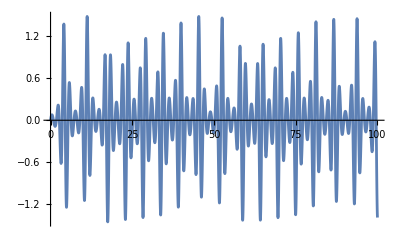

-Graphics3D-

{0,{0.1,0.,0.},1}

$Aborted

{-d y+x (-b+z),d x+y (-b+z),c+a z-z^3/3-(x^2+y^2) (1+e z)+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]}

$Aborted

(-b+z | -d | x
d | -b+z | y
-2 x (1+e z)+3 x^2 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]] | -2 y (1+e z)+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]] | a-e (x^2+y^2)-z^2+x^3 Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]])

Part::partd: Part specification $Aborted⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {$Aborted⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues[{{-b+z,-d,x},{d,-b+z,y},{-2 x (1+e z)+3 x^2 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]],-2 y (1+e z)+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]],a-e (x^2+y^2)-z^2+x^3 Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]]}}/.$Aborted⟦1⟧]

Eigenvalues[{{-b+z,-d,x},{d,-b+z,y},{x (-2-2 e z+3 x z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]+x^2 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]]),-2 (y+e y z)+x^3 z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]],a-e (x^2+y^2)-z^2+x^3 (Function[{a,b,c,d,e,f},Function[{t,x,y,z},{(z-b) x-d y,d x+(z-b) y,c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3}]]+z Function[{a,b,c,d,e,f},Function[{t,x,y,z},{{0,0,0},{0,0,0},{0,0,0}}]])}}/.$Aborted⟦1⟧]

```mathematica
f={a,b,c,d,e,f}|->{t,x,y,z}|->{
(z-b) x-d y,
d x+(z-b) y,
c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3};

{{rkf45=Module[{rkf45prime,β,α,c,cHat,cT},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
{f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,Sequence@@x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
]
];}, {□}}
(*Set parameters for the Aizawa attractor*)
params={0.95,0.7,0.6,3.5,0.25,0.1};

(*Initial conditions*)
initial={0,{0.1,0.0,0.0},1};
update=rkf45[f@@params,10^-6];
data=NestWhileList[update,initial,#[[1]]<100&];

(*Visualization*)
Map[{#[[1]],#[[2,2]]}&,data]//ListLinePlot
lpp=Map[#[[2]]&,data]//ListLinePlot3D[#,BoxRatios->{1,1,1},PlotRange->All,PlotStyle->{Thin}]&

state=initial
Dynamic@Show[lpp,Graphics3D[{Red,Sphere[state[[2]],0.05]}],ImageSize->Large]
While[True,state=update[state];Pause[0.0005]]

{
(z-b) x-d y,
d x+(z-b) y,
c+a z-z^3/3-(x^2+y^2) (1+e z)+f z x^3
}
Solve[Map[#==0&,%],{x,y,z}]
Grad[%%,{x,y,z}];
%//MatrixForm
%%/.%%%[[1]]//Eigenvalues
%/.r->1//FullSimplify//PowerExpand
```